```mathematica
Integrate[4x^3,x]
```

x^4

```mathematica
Integrate[3x,x]
```

(3 x^2)/2

```mathematica
Integrate[5+1/x^2,x]
```

-1/x+5 x

```mathematica
Integrate[Exp[-x],x]
```

-ⅇ^-x

```mathematica
Integrate[Exp[-x],{x,0,Infinity}]
```

1

Piecewise[{{0, x≤0}, {(3 x)/2-(3 x^2)/4+x^3/8, 0<x&&x<2}, {1, True}}]

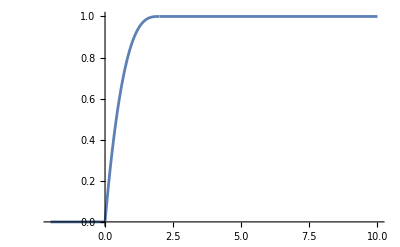

```mathematica
$Assumptions = x∈Reals;
F = Piecewise[{{0,x<=0},{1/8*x^3-3/4*x^2+3/2*x,0<x && x<2},{1,True}}]
Plot[F,{x,-2,10}]
```